FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{μ→139.332,σ→31.6661,k→174766.}

{μ→232.226,σ→7.9519,k→87051.7}

%% AMS-LaTeX Created by Wolfram Mathematica 9.0 : www.wolfram.com

\documentclass{article}
\usepackage{amsmath, amssymb, graphics, setspace}

\newcommand{\mathsym}[1]{{}}
\newcommand{\unicode}[1]{{}}

\newcounter{mathematicapage}
\begin{document}

\[2201.77 e^{-0.000498632 (-139.332+x)^2}\]

\end{document}

%% AMS-LaTeX Created by Wolfram Mathematica 9.0 : www.wolfram.com

\documentclass{article}
\usepackage{amsmath, amssymb, graphics, setspace}

\newcommand{\mathsym}[1]{{}}
\newcommand{\unicode}[1]{{}}

\newcounter{mathematicapage}
\begin{document}

\[4367.33 e^{-0.00790729 (-232.226+x)^2}\]

\end{document}

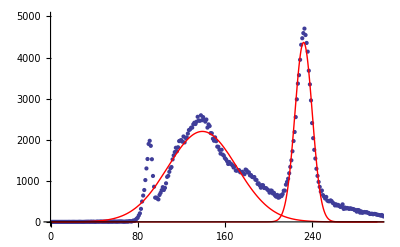

```mathematica
(*Clear unused stuff*)
Clear[ Filename, Filepath, rawBackground, rawData, BackgroundTime, DataTime, removeBackground];

(*Specify folder structure and filenames*)
Filename = "Cs137-1-no-bg";
Filepath = NotebookDirectory[]<>"../data/";

(*Import raw data from .Spe files*)
rawData = Import[Filepath<> Filename <>".txt", "Table"];
cutData = rawData;
(*remove unused lines and background influence from measurements*)
(*cutData = Take[Drop[Drop[rawData, 12],-14],400][[All, 1]];*)



(*Add channel numbers to counts and export as txt*)
(*cutData = MapIndexed[{First[#2], #1}&,cutData];*)

xraypeak = Take[cutData, {50,96}];
gammapeak = Take[cutData, {200,250}];

(*
xraypeak = Take[cutData, {50,120}];
gammapeak = Take[cutData, {200,250}];
*)

model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));


xrayfit=FindFit[xraypeak, model[x], {{μ, 90}, {σ, 4}, {k, 20000}}, x]
gammafit=FindFit[gammapeak, model[x], {{μ, 220}, {σ, 8}, {k, 90000}}, x]

xrayTeX = model[x]/.xrayfit;
gammaTeX = model[x]/.gammafit;

ExportString[xrayTeX, "LaTeX"]
ExportString[gammaTeX, "TeX"]



Show[{ListPlot[cutData, PlotRange->{{0,300}, {0, 5000}}], Plot[ model[x]/.xrayfit,  {x,0,400}, PlotStyle->Red, PlotRange->{{0,300}, {0, 5000}}],Plot[ model[x]/.gammafit,  {x,0,300}, PlotStyle->Red, PlotRange->{{0,300}, {0, 5000}}]}]
```